## Parámetros Comunes

```mathematica
ColoresTema=ColorData[106,"ColorList"];
```

## Redes

```mathematica
Folder="C:\\Users\\Rodrigo\\Desktop\\Tesis\\DAQ\\Datos_Para_Entrenamiento\\Genomas\\";
SetDirectory[Folder];
Run["dir /b > filename.txt"];
Files=Import["filename.txt","List"];
Etiquetas={"0"->"Sesgo","1"->"Tiempo","2"-> "Voltaje","3"->"Pos. Anterior","4"->"Pos. Angular"};
Complejidad={{"Nombre","Complejidad"}};
```

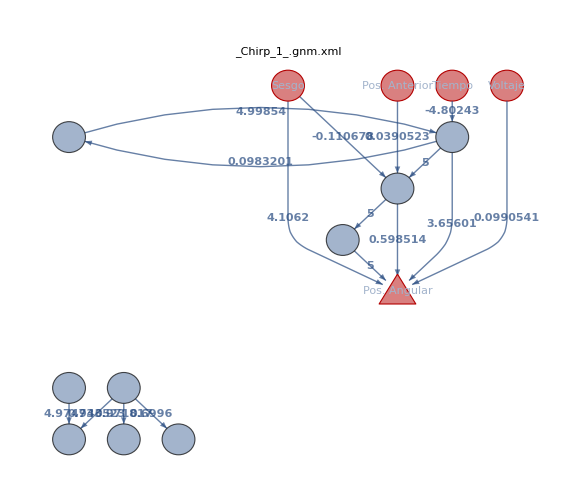

16

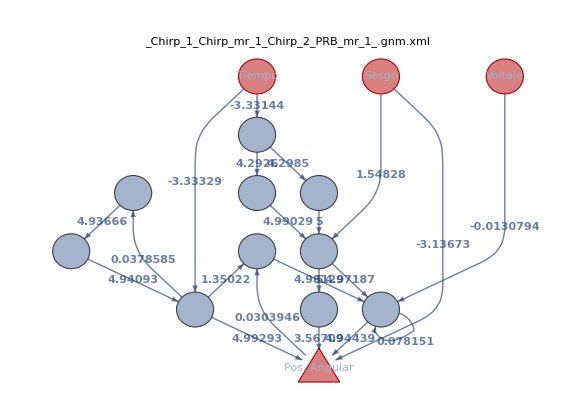

21

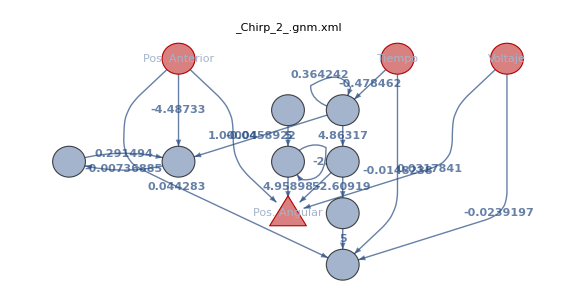

18

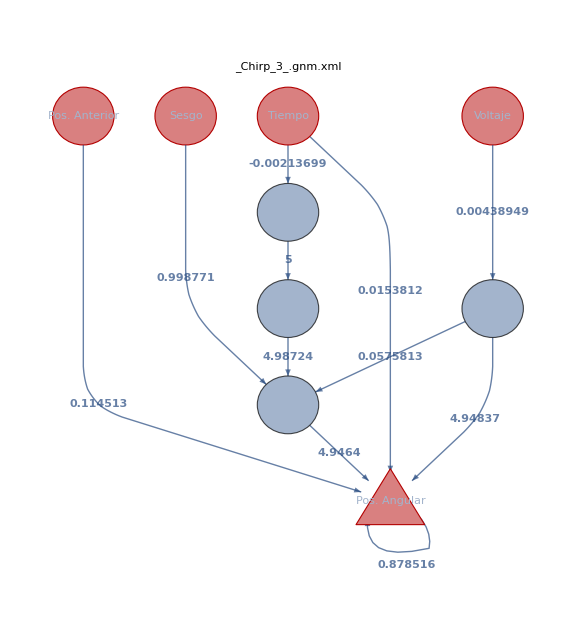

11

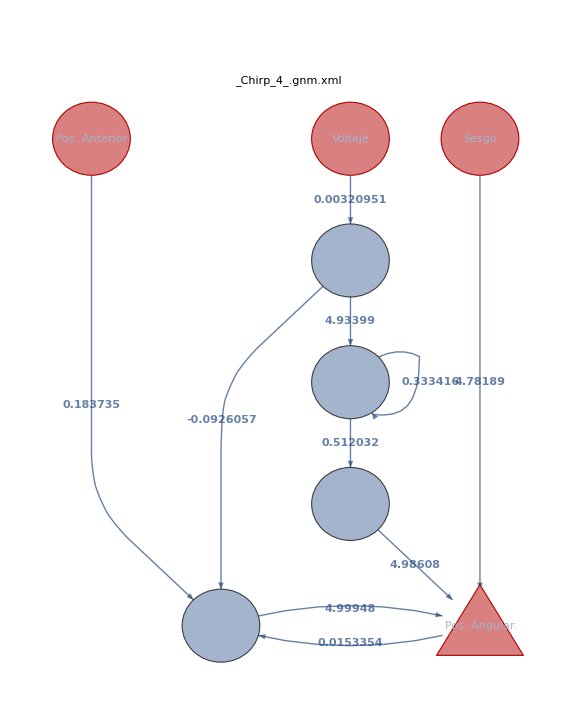

10

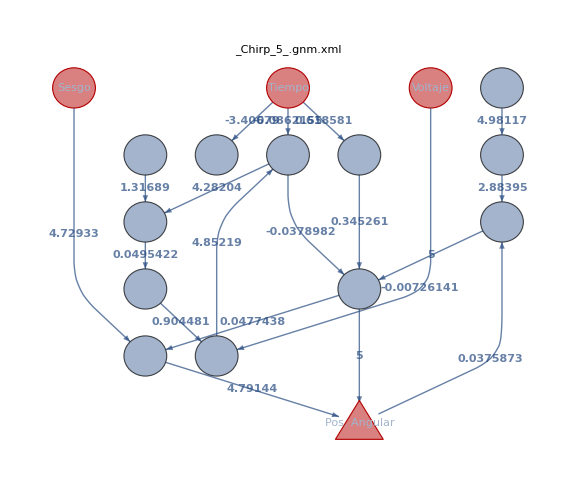

19

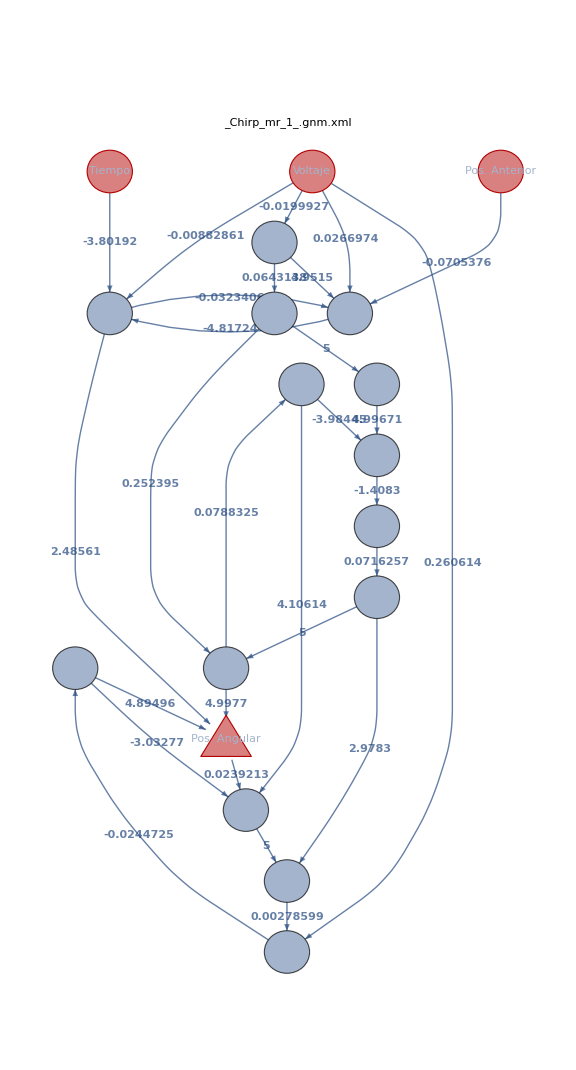

28

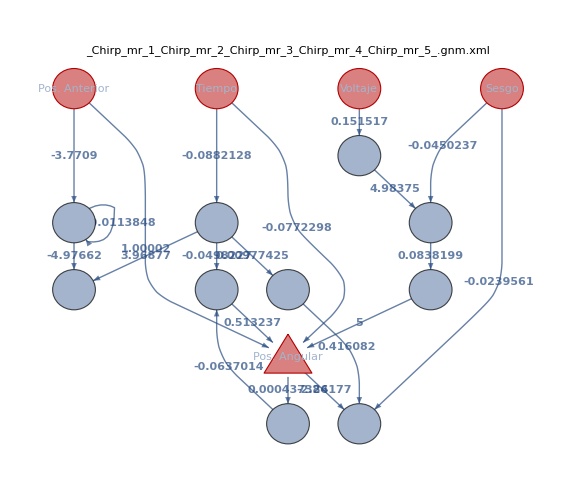

20

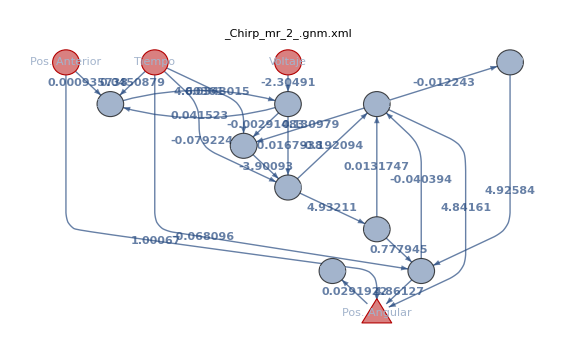

23

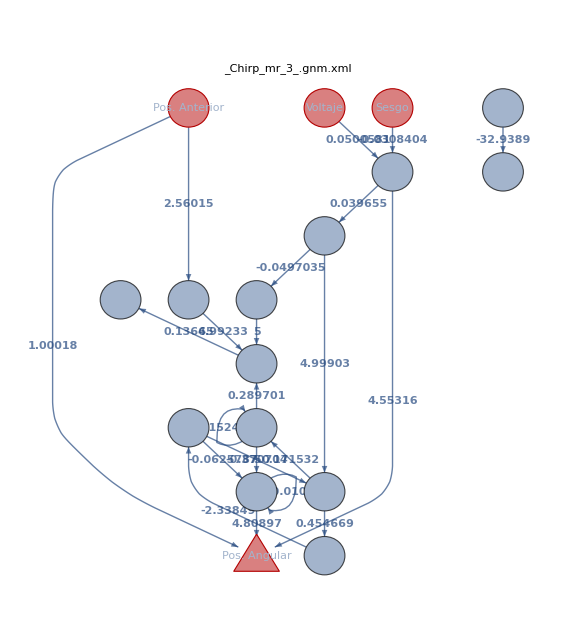

22

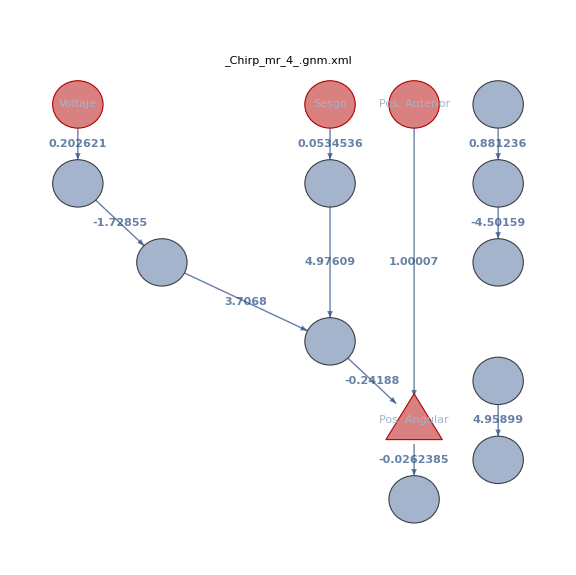

11

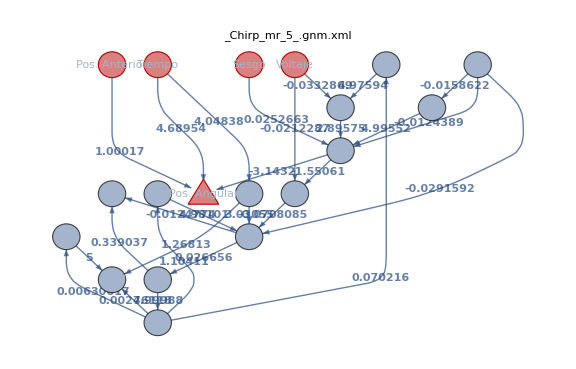

27

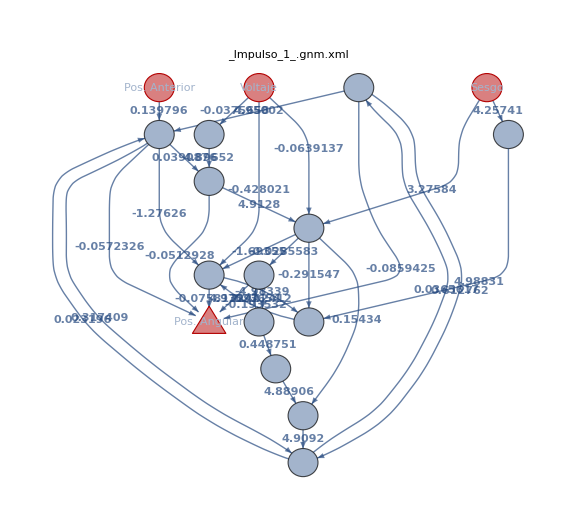

32

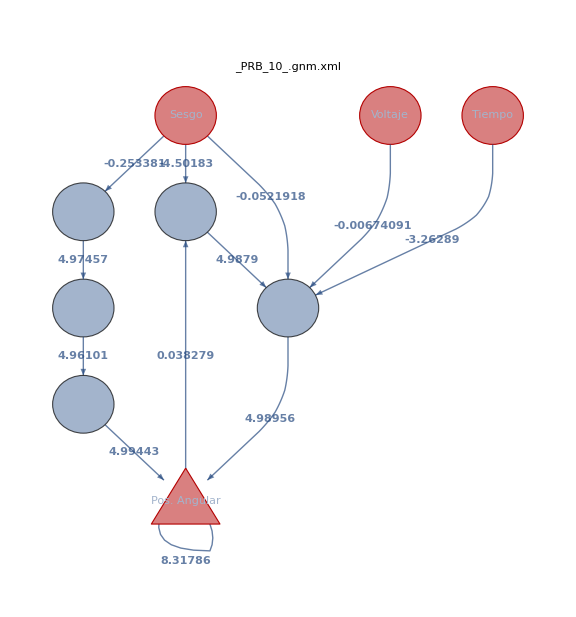

12

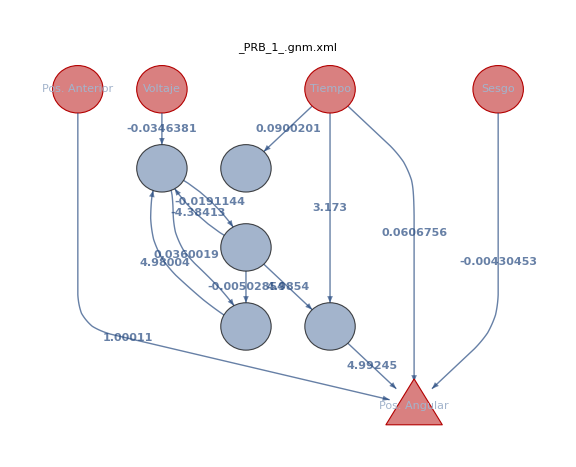

13

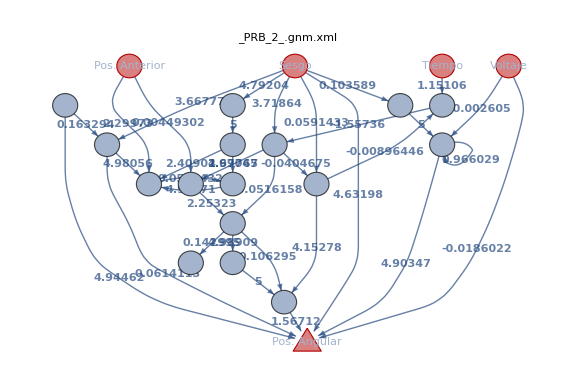

35

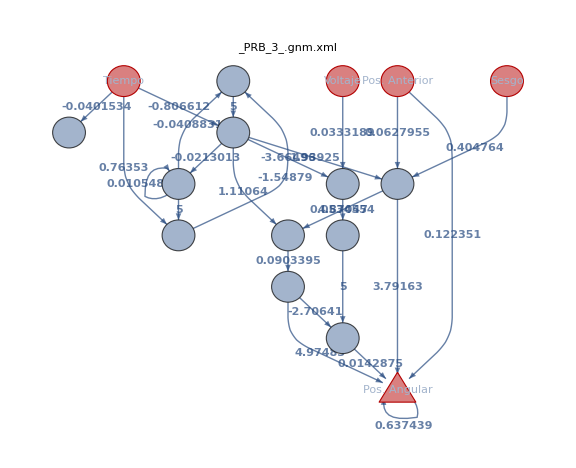

25

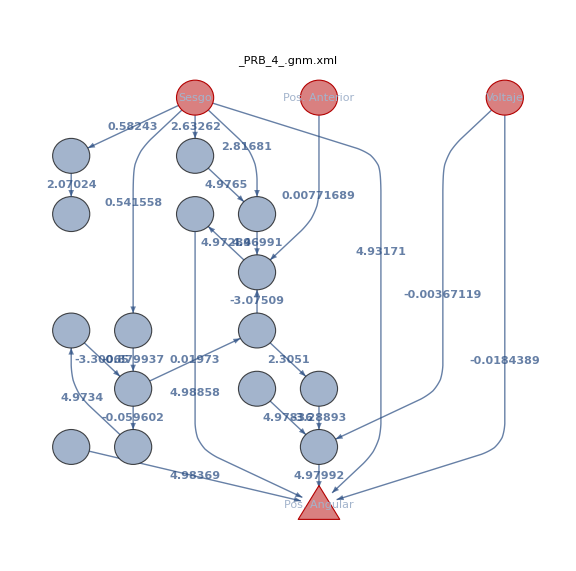

24

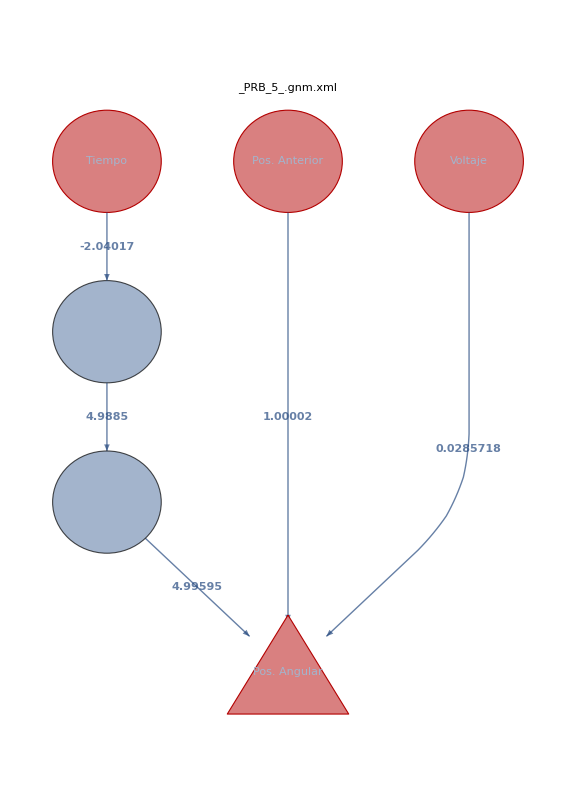

5

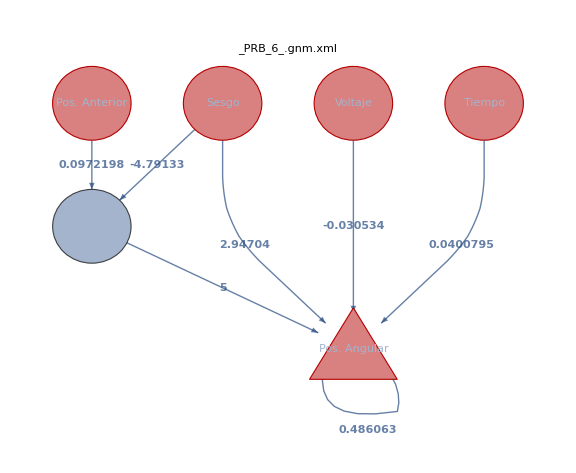

7

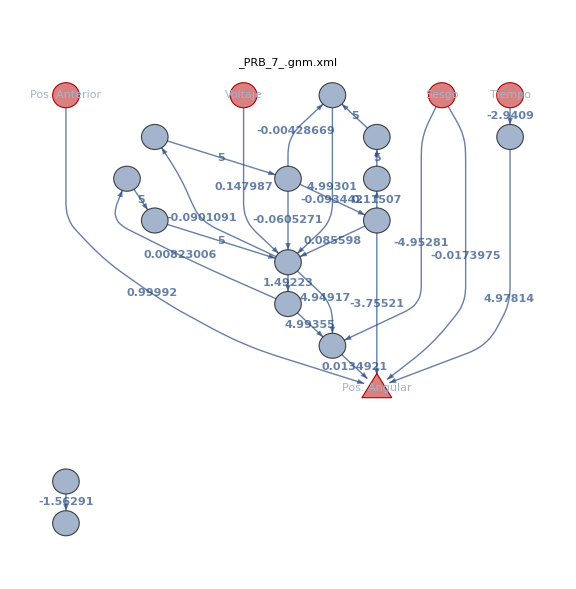

25

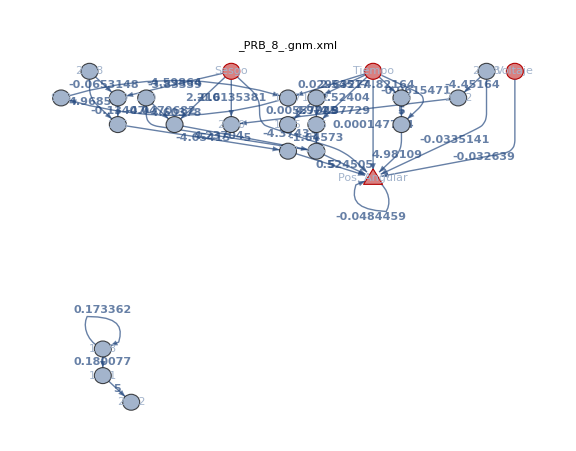

34

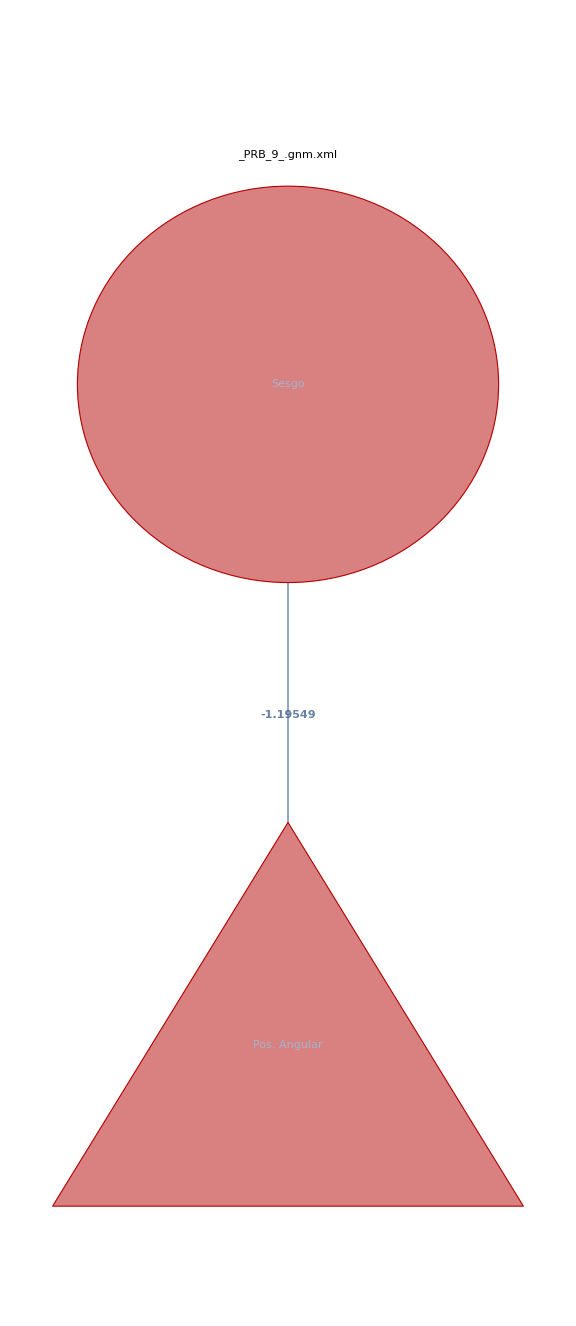

1

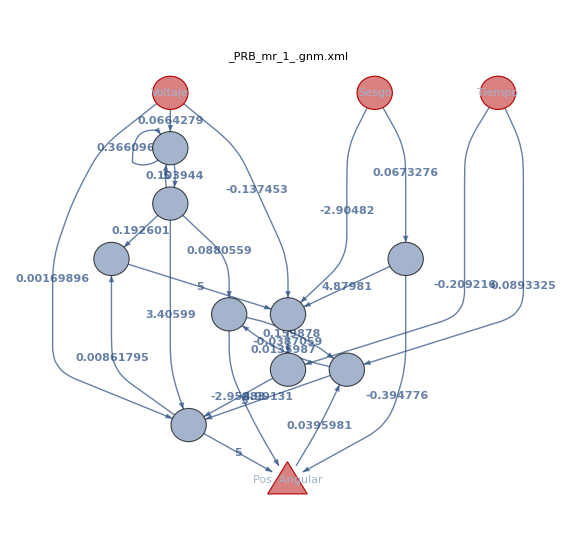

25

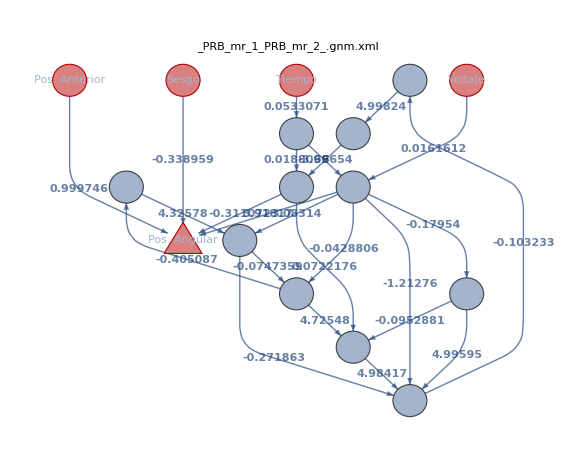

24

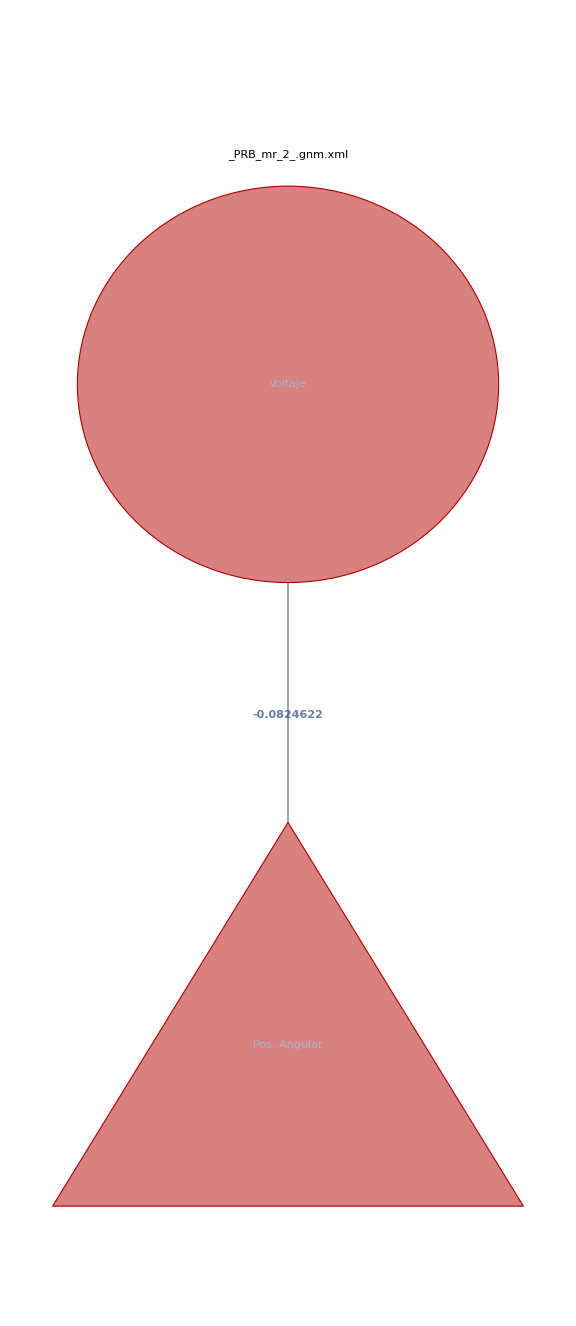

1

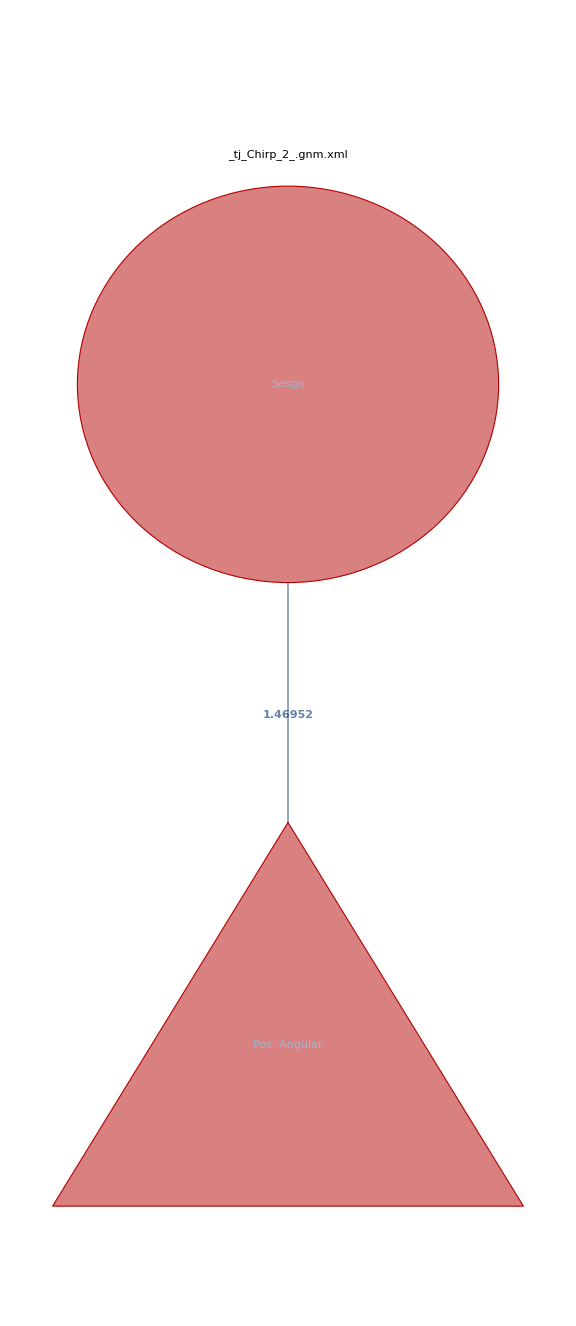

1

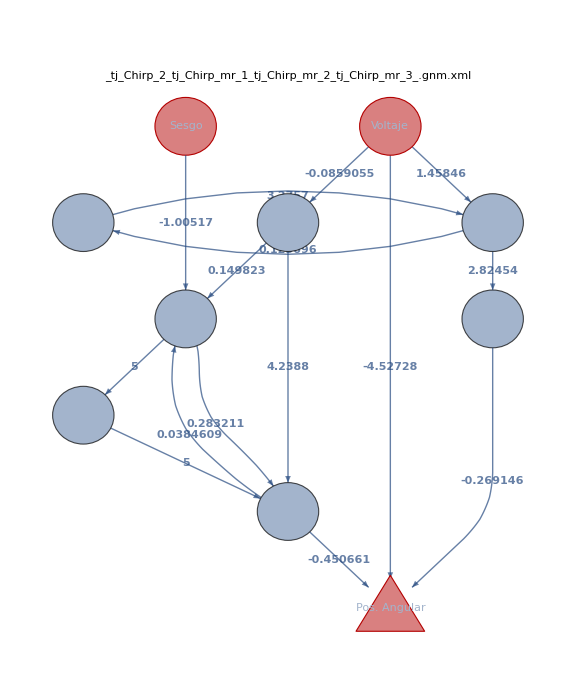

15

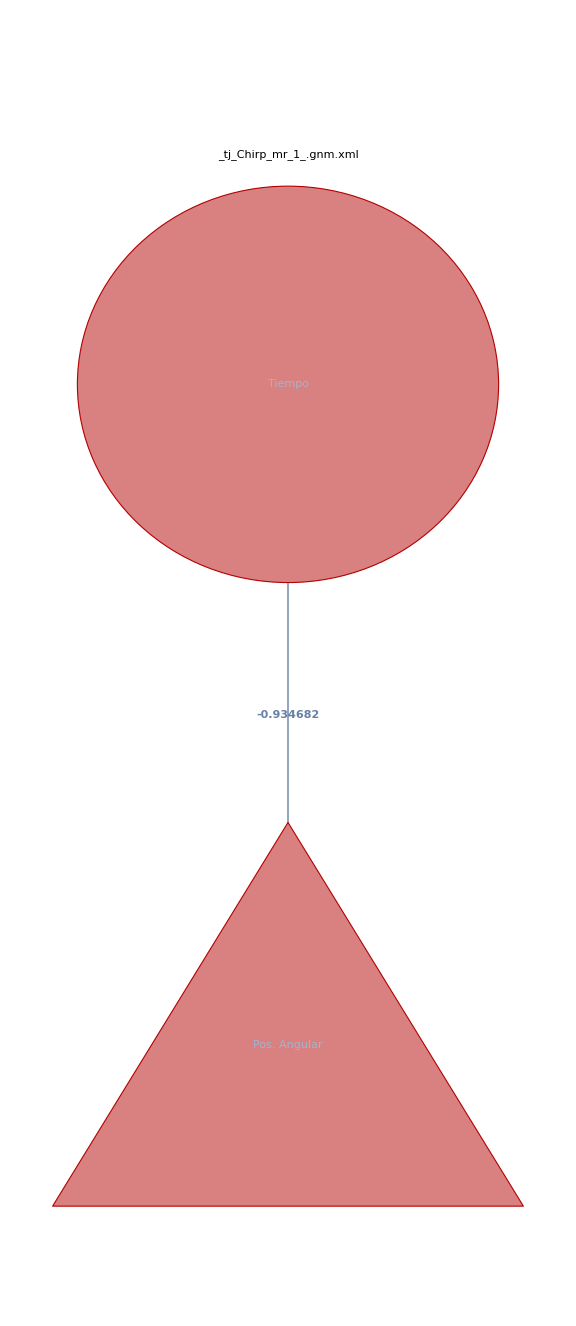

1

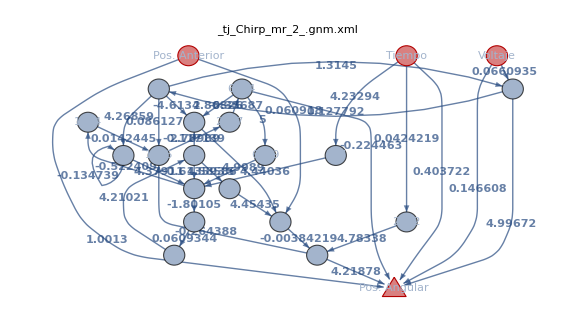

36

```mathematica
For[i=1,i<=Length[Files],i++,
If[StringCount[Files[[i]],".xml"]>0,
Genoma=Import[Files[[i]],"XML"];
Nodos=Cases[Genoma,XMLElement["Node",_,_],Infinity];
IdNodos=Nodos[[6;;,2]];
Cons=Cases[Genoma,XMLElement["Con",_,_],Infinity];
(*Coordenadas=Table[("id"-> {RandomInteger[{1,H-1}],RandomInteger[{1,H-1}]})/.IdNodos[[n]],{n,1,Length[IdNodos]}];*)
G=Table["src"->"tgt"/.Cons[[;;,2]][[n]],{n,1,Length[Cons]}]/.Etiquetas;
W=ToExpression[Table["wght"/.Cons[[;;,2]][[n]],{n,1,Length[Cons]}]];
Cuenta=Table[Count[G/.Rule->List//Flatten,ToString[n]/.Etiquetas],{n,0,3}];
roots={};
For[j=1,j<5,j++,
If[Cuenta[[j]]>0,
roots=Join[roots,{ToString[j-1]}]]
];
roots=roots/.Etiquetas;
NN=Graph[G/.Etiquetas,
(*VertexLabels->"Name",*)
VertexLabels->Placed["Name",{1/2,1/2}],
GraphHighlight->Join[roots,{"Pos. Angular"}],
VertexShapeFunction->{"Pos. Angular"->"Triangle"},
GraphHighlightStyle->"Thick",
DirectedEdges->True,
GraphLayout->{"LayeredDigraphDrawing","RootVertex"->roots},
VertexSize->0.6,
ImageSize->Large,
EdgeWeight->W,
EdgeLabels->"EdgeWeight",
EdgeLabelStyle->Directive[DefaultPrintPrecision->3,Bold],
PlotLabel->Files[[i]]
];
Print[NN];
Print[Length[Cons]];
Complejidad=Join[Complejidad,{{StringReplace[Files[[i]],".gnm.xml"->""],Length[Cons]}}];
];
]
```